# Math 223: Homework 10

<Hardeep Bassi>

<04/21/2023>

## Problem 1

Use boundary-layer theory to find a uniform approximation with error of order  for the problem:
. Notice that there is no boundary layer in leading order, but one does appear in next order. Compare your solution with the exact solutions to this problem.

To solve for the outer layer, we proceed by letting  . Upon substitution into the perturbed ODE, we see that:
 which means that . Our boundary condition of , then tells  us that . Hence, the  approximation is given by . To find the next order, we proceed:
.

```mathematica
DSolve[{y'[x] + y[x] ==- E^(-x+1), y[1] == 0}, y[x], x]
```

{{y[x]→-ⅇ^(1-x) (-1+x)}}

This means that we get the  approximation as .

To compute the inner solution, we introduce the stretched variable . Plugging this into the ODE yields:
. Now let . We see that . Solving this ODE yields:

```mathematica
DSolve[{y''[X]+y'[X]==0, y[0]==E}, y[X],X]
```

{{y[X]→ⅇ^-X (ⅇ^(1+X)-C[1]+ⅇ^X C[1])}}

In general,we see that  Solving this ODE yields:

```mathematica
DSolve[{y''[X]+y'[X] == -z[X], y[0] == 0}, y[X], X]
```

{{y[X]→(ⅇ^(-K[2]) C[1]+ⅇ^(-K[2]) -ⅇ^K[1] z[K[1]]K[1]0K[2])K[2]0X}}

This shows that:

Now, we must perform asymptotic matching:

We see that  and that . Hence,  and so . Looking back at our expression for , we can seek a Taylor expansion to show:

```mathematica
Series[E^(-X+1),{X,0,4}]
```

ⅇ-ⅇ X+(ⅇ X^2)/2-(ⅇ X^3)/6+(ⅇ X^4)/24+O[X]^5

Hence, we see that: . By looking at our above expressions, we can obtain :

.
This means that . Hence, , which means  as . This means that

```mathematica
AsymptoticApproxP1[x_,ϵ_] =  -ϵ*E^(1-x/ϵ) + E^(-x+1) - ϵ*E^(-x+1)*(x-1)
```

ⅇ^(1-x)-ⅇ^(1-x/ϵ) ϵ-ⅇ^(1-x) (-1+x) ϵ

```mathematica
DSolve[{0.01y''[x]+y'[x]+y[x] == 0, y[0] == E, y[1] == 1}, y[x], {x,0,1}]
```

{{y[x]→-0.0278825 ⅇ^(-98.9898 x)+2.74616 ⅇ^(-1.01021 x)}}

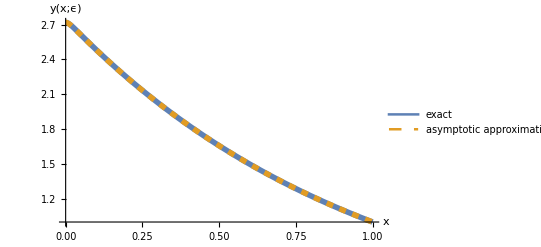

```mathematica
Plot[{-0.027882488833381434 ⅇ^(-98.98979485566356 x)+2.746164317292426 ⅇ^(-1.0102051443364388 x),AsymptoticApproxP1[x,0.01]},{x,0,1},PlotLegends->{"exact","asymptotic approximation"},PlotRange->All,PlotStyle->{ Directive[Solid,Thickness[0.01]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["y(x;ϵ)", Italic, 18]}, TicksStyle->Directive[FontSize->14]]
```

## Problem 2

Use boundary -layer methods to find an approximate solution to the initial-value problem . Show that the leading order uniform approximation satisfies , but not  for arbitrary . Compare the leading-order uniform approximation with the exact solution to the problem when  and  are constants.

To solve for the outer layer, we proceed by letting  . Upon substitution into the perturbed ODE, we see that .  This has solution:

```mathematica
DSolve[{a[x]*y'[x]+b[x]*y[x] == 0}, y[x], x,Assumptions->{a[x] > 0, b[x] > 0, x >= 0}]
```

{{y[x]→ⅇ^(-b[K[1]]/a[K[1]]K[1]1x) C[1]}}

Hence,  Cⅇ^(-b[K[1]]/a[K[1]]K[1]1x) .
To compute the inner solution, we introduce the stretched variable . Plugging this into the ODE yields:
. This has solution:

```mathematica
DSolve[{y''[X] + a[x]*y'[X] == 0, y[0] == 1, y'[0] ==1}, y[X],X]//FullSimplify //Expand
```

{{y[X]→1+1/a[x]-ⅇ^(-X a[x])/a[x]}}

This means that  1+1/a[x]-ⅇ^(-X a[x])/a[x]. 
Now, we must perform asymptotic matching: 
. Looking back at our definitions of  yields:
 for the given choice of . 
This means that

Now, we take

```mathematica
NumericalSolution =DSolve[{0.01y''[x]+ 1*y'[x]+1*y[x]==0,y[0]==1,y'[0]==1},y[x],{x,0,1}]
```

{{y[x]→-0.0205166 ⅇ^(-98.9898 x)+1.02052 ⅇ^(-1.01021 x)}}

```mathematica
AsymptoticApproxP2[x_,ϵ_] =  E^(-1)*E^((1-x))+ 1-Exp[-x/ϵ]
```

1+ⅇ^-x-ⅇ^(-x/ϵ)

```mathematica
AsymptoticApproxP2[0,0.01]
```

1.

Computing the derivative, we see that . This means that , when

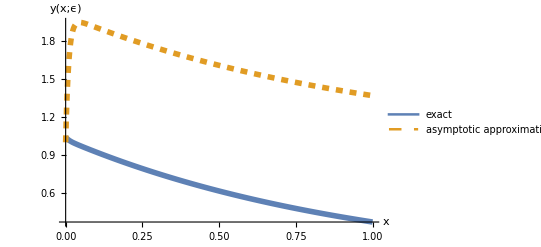

```mathematica
Plot[{0.020516570341425348 ⅇ^(-98.98979485566356 x)+1.0205165703414252 ⅇ^(-1.0102051443364388 x),AsymptoticApproxP2[x,0.01]},{x,0,1},PlotLegends->{"exact","asymptotic approximation"},PlotRange->All,PlotStyle->{ Directive[Solid,Thickness[0.01]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["y(x;ϵ)", Italic, 18]}, TicksStyle->Directive[FontSize->14]]
```

Which was bound to fail as suggested by the problem.

## Problem 3

The function  satisfies  and is subject to boundary conditions  and . Find two terms in the outer approximation, applying only the boundary condition at . Next find two terms in the inner approximation for the boundary layer near , which can be assumed to have width , and applying only the boundary condition at . Finally determine the constants of integration in the inner approximation by matching.
To solve for the outer layer, we proceed by letting  . Upon substitution into the perturbed ODE, we see that .  This has solution known solution . For the higher order solutions, we see that:

```mathematica
DSolve[{y'[x] + y[x] == 0, y[0] == 0}, y[x],x]
```

{{y[x]→0}}

Hence, . 

To compute the inner solution, we introduce the stretched variable  and assume that . We see that:  and .

```mathematica
DSolve[{y''[x] + y'[x] == 0, y[0] == 0}, y[x],x]
```

{{y[x]→ⅇ^-x (-1+ⅇ^x) C[1]}}

For the higher order solution:

```mathematica
DSolve[{y''[X]+y'[X] == -Exp[-X]-(1-Exp[-X]), y[0] ==0},y[X],X]
```

{{y[X]→-ⅇ^-X (ⅇ^X X+C[1]-ⅇ^X C[1])}}

This means that we have:

Now, we must perform asymptotic matching:
We see that  and that . Hence, , so . For , we see that:
. This means that .
Putting all this together means that

```mathematica
NumericalSol =DSolve[{0.01*y''[x]+(1+0.01)*y'[x]+y[x]==0,y[0]==0,y[1]==Exp[-1]},y[x],{x,0,1}]
```

{{y[x]→-1. ⅇ^(-100. x)+1. ⅇ^(-1. x)}}

```mathematica
AsymptoticApproxP3[x_,ϵ_] =  Exp[-x]- Exp[-x/ϵ]
```

ⅇ^-x-ⅇ^(-x/ϵ)

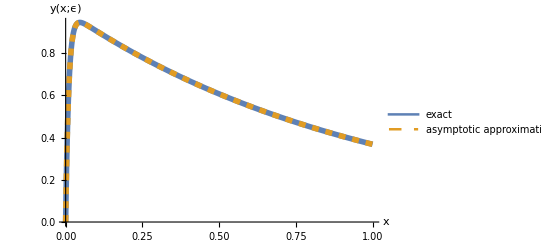

```mathematica
Plot[{-1. ⅇ^(-100. x)+1. ⅇ^(-1. x),AsymptoticApproxP3[x,0.01]},{x,0,1},PlotLegends->{"exact","asymptotic approximation"},PlotRange->All,PlotStyle->{ Directive[Solid,Thickness[0.01]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["y(x;ϵ)", Italic, 18]}, TicksStyle->Directive[FontSize->14]]
```

credit to Irabiel for assistance on the asymptotic matching for this problem.